```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica/good_fits

```mathematica
LECsNUCL=Import["../LECs_nucl_Joki.dat","Table"][[2;;]];

activeLEC=LECsNUCL[[All,{1,2,3}]];
hbar=197.327053;
Mm=938.92;
m1=2 Mm;m2= Mm;
μ=m1 m2/(m1+m2);
mh2=(2Mm)/(hbar)^2;
Print[1/mh2]
```

20.7355

```mathematica
I1[lam_,b1_,b2_] :=(Pi/(2b1+2b2+4 lam))^(3/2);
I2[lam_,b1_,b2_] := 0;
I3[b1_,b2_] :=3 b1 b2 Pi^(3/2)/(2^(3/2)(b1+b2)^(5/2));
```

```mathematica
ham[lam_,b1_,b2_]:=Module[{locall=lam},
LECc = Flatten[Select[activeLEC,#[[1]]==locall&]][[2]];
LECd = Flatten[Select[activeLEC,#[[1]]==locall&]][[3]];
LECc I1[0.25 lam^2,b1,b2]+LECd I2[0.25 lam^2,b1,b2]+(1/mh2)I3[b1,b2]
]  ;
norm[b1_,b2_]:=Module[{},(Pi/(2b1+2b2))^(3/2)
]  ;
```

dimD:  bare basis dimension
widths: educated guess for the Gaussian width parameters each of which defines a bare basis function  e^(-β∑(r̄)^2)
lamd: cutoff/regularization parameter of the interaction
evlowthreshold: empirically determined threshold which sets the lower bound for the norm eigenvalues that are allowed in the
                                   stable, reduced basis

```mathematica
1/#&/@PowerRange[1,600,3-1/dimD]
```

{1,1/3,1/9,1/27,1/81,1/243}

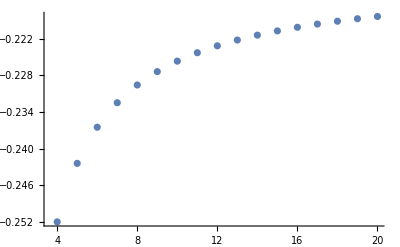

```mathematica
results={};
SetSharedVariable[results];


maxDim=20;
ParallelDo[

widths=N[1/#&/@PowerRange[4,600000,3-1/nn]];
dimD=Length[widths];
lamd=4;
evlowthreshold=10^-10;

hamm=Table[ham[lamd,widths[[i]],widths[[j]]],{i,dimD},{j,dimD}];
normm=Table[norm[widths[[i]],widths[[j]]],{i,dimD},{j,dimD}];

esn=Eigensystem[normm];

(* norm eigensystem in descending eigenvalue order *)
{μ,transf}=Transpose[Select[Sort[Transpose[esn],#1[[1]]<#2[[1]]&],#[[1]]>evlowthreshold&]];
(* define transformation such that norm matrix in this basis is the unit matrix Subscript[δ, ij] *)
trafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);

(* transfrom Hamiltonian *)
traham=(Transpose[trafma].hamm).trafma;

(* compare results in bare and stable basis spaces and ecce that the stable basis is orthogonal and hence
we solve just an ordinary eigenvalue problem *)
evbare=Sort[Eigensystem[{hamm,normm}][[1]],Re[#1]<Re[#2]&][[1]];
evstable=Sort[Eigensystem[traham][[1]],#1<#2&][[1]];
AppendTo[results,{nn,evbare}];
,{nn,Range[4,maxDim,1]}];
ListPlot[results]
```

```mathematica
traham//MatrixForm;
normm//MatrixForm;

IsReal=Select[(#∈Reals)&/@evstable,#==False&];

Print["Norm matrix is positive definite?  ",PositiveDefiniteMatrixQ[normm]]
Print["Hamiltonian is hermitian?  ",HermitianMatrixQ[Chop[traham]]]
Print["There are complex eigenvalues?  ",IsReal!={}]
```

Norm matrix is positive definite?  False

Hamiltonian is hermitian?  False

There are complex eigenvalues?  False

```mathematica
Chop[traham-Transpose[traham],10^-6]//MatrixForm;
```

Hamiltonian is hermitian?  False

There are complex eigenvalues?  False

Norm matrix is positive definite?  False

Hamiltonian is hermitian?  False

There are complex eigenvalues?  False

Norm matrix is positive definite?  False

Hamiltonian is hermitian?  False

There are complex eigenvalues?  False